# Minimize MNIST linear layer

## Load data

Generated from generate_small_mnist.py

```mathematica
XY=N[Import["~/git/whitening/exp/mnist_small.csv"]];
f1 = 50; (* first layer *)
f2=10; (* second layer *)
dsize=XY//Dimensions//Last; (* batch dimension *)
X=XY[[;;f1]];
Y=XY[[f1+1;;]];

(* center the data (don't center, that gets rid of bias *)
(* Xc=Mean[Transpose@X];
X=Transpose[#-Xc&/@Transpose[X]];*)

(* Predict 0.1 for every class *)
W0=Join[Array[0.&,{f2,f1-1}],Array[0.1&,{f2,1}],2];
error0=(W0.X-Y);
Tr[error0.error0ᵀ]
```

900.

## Least squares solution

```mathematica
Wt=Y.Xᵀ.PseudoInverse[X.Xᵀ];
errort=(Wt.X-Y);
Wtf =vectorize[Wt];
Tr[errort.errortᵀ]
```

417.73

```mathematica
(* Compute 0-1 error for given parameter vector *)
errorCount[Wt_]:=Module[{},
predictions=Wt.X;
winningScores=Max/@Transpose[predictions];
winningPositions=MapThread[First[Flatten[Position[#1,#2]]]&,{predictionsᵀ,winningScores}]//Flatten;

winningScores2=Max/@Transpose[Y];
truePositions=MapThread[Position[#1,#2]&,{Yᵀ,winningScores2}]//Flatten;
errorList=MapThread[If[#1==#2,0,1]&,{winningPositions,truePositions}];
Total@errorList
];
errorCountf[Wtf_]:=errorCount@unvectorize@Wtf
```

## Iteratively get least squares solution

```mathematica
Clear[W,Wf];
grad[W_]:=2(W.X-Y).Xᵀ/dsize;

(* column vectorize, following Magnus, 1999 *)
vectorize[W_]:=Transpose@{Flatten@Transpose[W]}
unvectorize[Wf_]:=Transpose[Flatten/@Partition[Wf,f2]]

err[W_]:=(W.X-Y);
loss[W_]:=Tr[err[W].err[W]ᵀ/dsize]
errf[Wf_]:=(unvectorize[Wf].X-Y);
lossf[Wf_]:=Tr[errf[Wf].errf[Wf]ᵀ/dsize]
gradf[Wf_]:=vectorize@grad@unvectorize@Wf; 

(*lossf[Wf_]:=*)
Print["Loss at W0 ",loss[W0]];
Print["Lossf at W0 ",lossf[vectorize[W0]]];
cov=X.Xᵀ/dsize;
```

Loss at W0 0.9

Lossf at W0 0.9

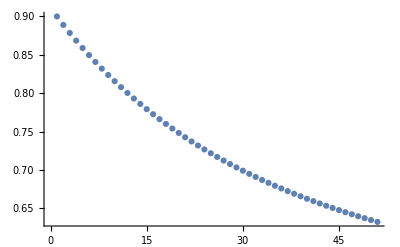

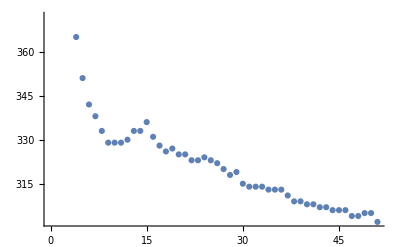

```mathematica
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimize[loss_,grad_,w0_,pre_,lr_]:=Module[{gradstep},
gradstep[w_]:=w-lr*grad[w].pre;
points=NestList[gradstep,w0,50];
loss/@points
];

pre=IdentityMatrix@f1;
losses0=optimize[loss,grad,W0,pre,1*^-6];
errors0=errorCount/@points;
ListPlot@losses0
ListPlot@errors0
```

```mathematica
Export["~/git/whitening/exp/mnist_linear_losses0.csv",losses0];
Export["~/git/whitening/exp/mnist_linear_errors0.csv",errors0];
```

## Optimization in vectorized form

```mathematica
(* since our gradients are column vectors, pre-condition multiply on left *)
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: pointsf *)
optimizef[loss_,grad_,w0_,pre_,lr_]:=Module[{gradstep},
gradstep[w_]:=w-lr*pre.grad[w];
pointsf=NestList[gradstep,w0,50];
loss/@pointsf
];

W0f=vectorize@W0;
pre=IdentityMatrix@500;
losses0=optimizef[lossf,gradf,W0f,pre,1*^-6];
ListPlot@losses0
ListPlot[errorCountf/@pointsf]
```

-Graphics-

-Graphics-

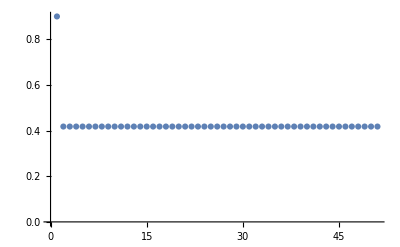

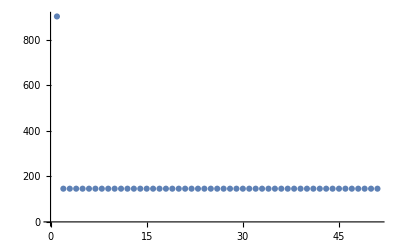

```mathematica
W0f=vectorize@W0;
pre=Inverse[(2X.Xᵀ/dsize)⊗IdentityMatrix[f2]];
losses1=optimizef[lossf,gradf,W0f,pre,1];
ListPlot@losses1
ListPlot[errorCountf/@pointsf]
```

## Newton' s step in unvectorized form

```mathematica
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimize[loss_,grad_,w0_,pre_,lr_]:=Module[{gradstep},
gradstep[w_]:=w-lr*grad[w].pre;
points=NestList[gradstep,w0,50];
loss/@points
];

pre=IdentityMatrix@f1;
losses1=optimize[loss,grad,W0,Inverse[(2X.Xᵀ/dsize)],1];
errors1=errorCount/@points;
ListPlot@losses0
ListPlot@errors0
```

-Graphics-

-Graphics-

```mathematica
Export["~/git/whitening/exp/mnist_linear_losses1.csv",losses1];
Export["~/git/whitening/exp/mnist_linear_errors1.csv",errors1];
```

```mathematica
losses1
```

{0.9,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773,0.41773}

## Get Newton’s decrement

```mathematica
observedChange=lossf[W0f]-lossf[Wtf];
λ[x0_,hess0_]:=toscalar[(gradf[x0]ᵀ.Inverse[hess0].gradf[x0])^(1/2)];
hess0=(2X.Xᵀ/dsize)⊗IdentityMatrix[f2];
expectedChange=1/2 λ[W0f,hess0]^2;
observedChange==expectedChange
```

True

```mathematica
loss[W0]
```

0.9